Question 1

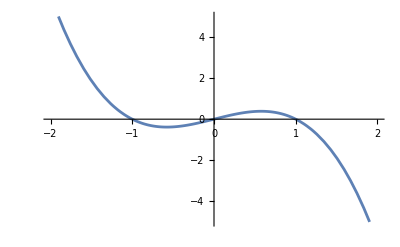

```mathematica
Plot[{x-x^3},{x,-2,2},PlotRange->{-5,5}]
(*
equilibrium poitns are 1 nd -1.
*)
```

Question 2

```mathematica
Integrate[{x (1-x),r-x-x^3,x (x-1) (x-2),x^2 (6-x),Tan[x], Log[x]},x]
```

{x^2/2-x^3/3,r x-x^2/2-x^4/4,x^2-x^3+x^4/4,2 x^3-x^4/4,-Log[Cos[x]],-x+x Log[x]}

```mathematica
Manipulate[Plot[Integrate[{x (1-x),r-x-x^3,x (x-1) (x-2),x^2 (6-x),Tan[x], Log[x]},x],{x,-8,8},PlotLegends->"Expressions",PlotRange->{-5,5},PlotStyle->{Thick,Thin}],{r,-5,5}]
```

Integrate::ilim: Invalid integration variable or limit(s) in -7.99967.

Integrate::ilim: Invalid integration variable or limit(s) in -7.67314.

Integrate::ilim: Invalid integration variable or limit(s) in -7.34661.

General::stop: Further output of Integrate::ilim will be suppressed during this calculation.

```mathematica
(*
1. x(1-x) stable equillibrium point is 1.
2. r-x-x^3 the point depends on teh value of r, but it would be an unstable fixed point, as on eiher side the function would tend to infinity.
3. x(x-1)(x-2), 0 and 2 are stable fixed points, while 1 is an unstable fixed point.
4. x^2(6-x), 0 is a stable fixed point, and 6 is an unstbale fixed point.
5. tan(x) has many equillibrium points, but neither of them are stable.
6. log(x) it has 1 fixed point, @x=1, and it's unstable.
*)
```

Question 3

```mathematica
Manipulate[Plot[-a n Log[b n],{n,.01,10}],{a,0.01,10},{b,.01,10}]
```

```mathematica
Solve[-a n Log[b n]==0,n]
```

{{n→1/b}}

```mathematica
func=Integrate[-a n Log[b n],n]
```

-a (-n^2/4+1/2 n^2 Log[b n])

```mathematica
Manipulate[Plot[-a (-n^2/4+1/2 n^2 Log[b n]),{n,.01,10}],{a,-10,10},{b,.01,10}]
```

```mathematica
Solve[func==0,n]
(*
roots of both the equations are unstable, and hence are unstable fixed poitns.
*)
```

{{n→(√ⅇ)/b}}

Question 4

```mathematica
Div[{xy,yz,0},{x,y,z}]
Curl[{xy,yz,0},{x,y,z}]
```

0

{0,0,0}

```mathematica
Div[{(x^2+y^2),(x^2-y^2),0},{x,y,z}]
Curl[{(x^2+y^2),(x^2-y^2),0},{x,y,z}]
```

2 x-2 y

{0,0,2 x-2 y}

Question 5

```mathematica
B={(2z x+x y),(2z y+y^2) ,(2z^2−x^2−y^2)}/((x^2+y^2+z^2)^(5/2 ))
```

{(x y+2 x z)/((x^2+y^2+z^2)^(5/2)),(y^2+2 y z)/((x^2+y^2+z^2)^(5/2)),(-x^2-y^2+2 z^2)/((x^2+y^2+z^2)^(5/2))}

```mathematica
VectorPlot3D[B,{x,-5,5},{y,-5,5},{z,-5,5},PlotLegends->Automatic]
```

-Graphics3D-

Question 6

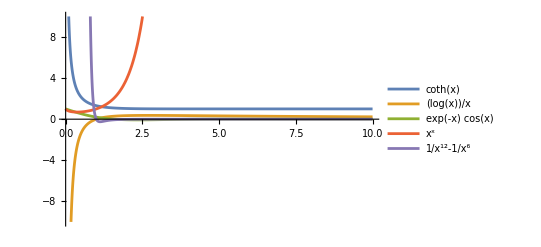

```mathematica
Plot[{Coth[x],Log[x]/x,Exp[-x]Cos[x],x^x,1/x^12-1/x^6},{x,0,10},PlotRange->{-10,10},PlotLegends->"Expressions"]
```